```mathematica
ssefsin=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_sin.dat"];
error=Table[{ssefsin[[i,1]],Log[10,Abs[Sin[ ssefsin[[i,1]]]- ssefsin[[i,2]]]]}, {i,1,ssefsin//Length}];
```

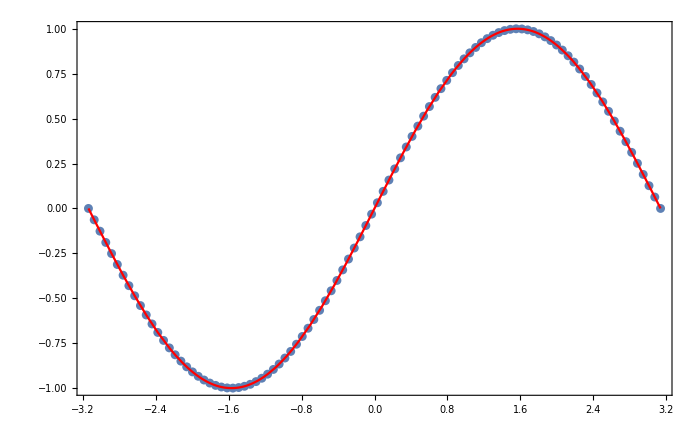

```mathematica
Show[
ListPlot[ssefsin, PlotRange->All, Frame->True, ImageSize->700],
Plot[Sin[x],{x,-Pi,Pi}, PlotStyle->Red]
]
```

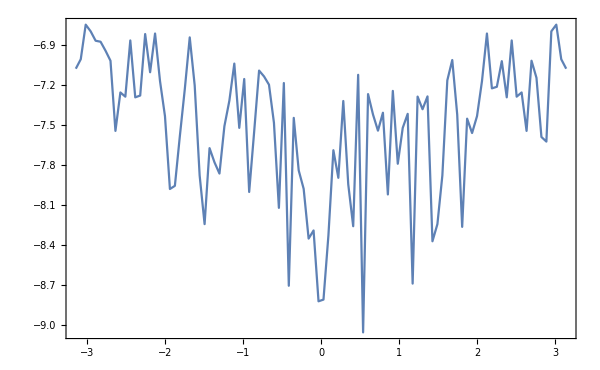

```mathematica
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

```mathematica
ssefcos=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_cos.dat"];
error=Table[{ssefcos[[i,1]],Log[10,Abs[Cos[ ssefcos[[i,1]]]- ssefcos[[i,2]]]]}, {i,1,ssefcos//Length}];
```

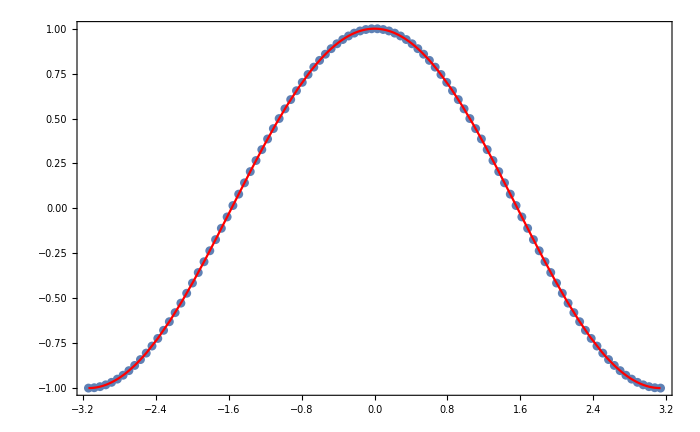

```mathematica
Show[
ListPlot[ssefcos, PlotRange->All, Frame->True, ImageSize->700],
Plot[Cos[x],{x,-Pi,Pi}, PlotStyle->Red]
]
```

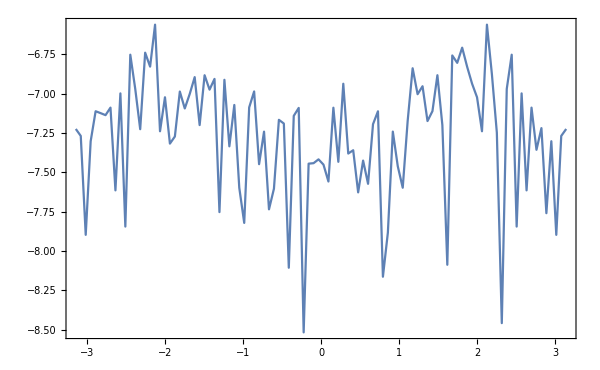

```mathematica
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

```mathematica
sseftan=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_tan.dat"];
error=Table[{sseftan[[i,1]],Log[10,Abs[Tan[ sseftan[[i,1]]]- sseftan[[i,2]]]]}, {i,1,ssefsin//Length}];
```

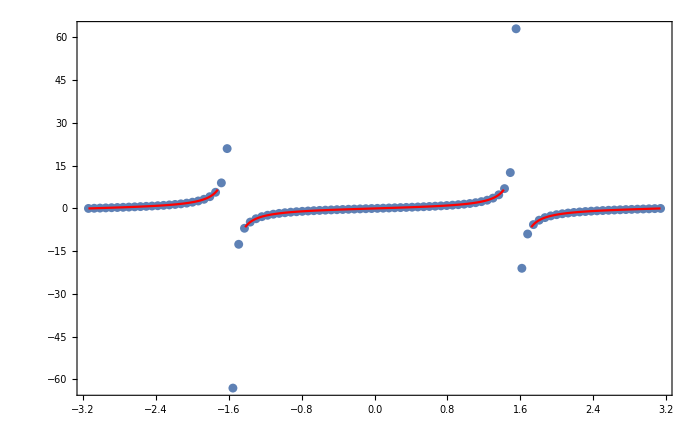

```mathematica
Show[
ListPlot[sseftan, PlotRange->All, Frame->True, ImageSize->700],
Plot[Tan[x],{x,-Pi,Pi}, PlotStyle->Red]
]
```

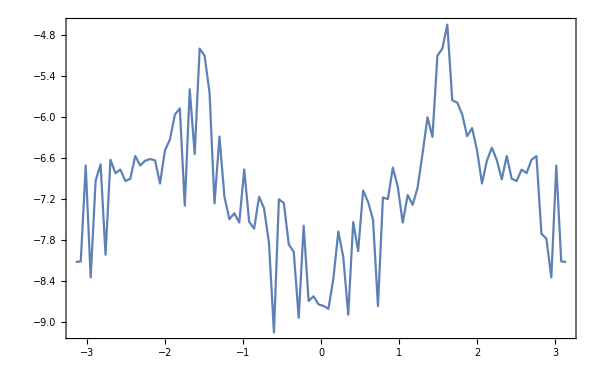

```mathematica
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

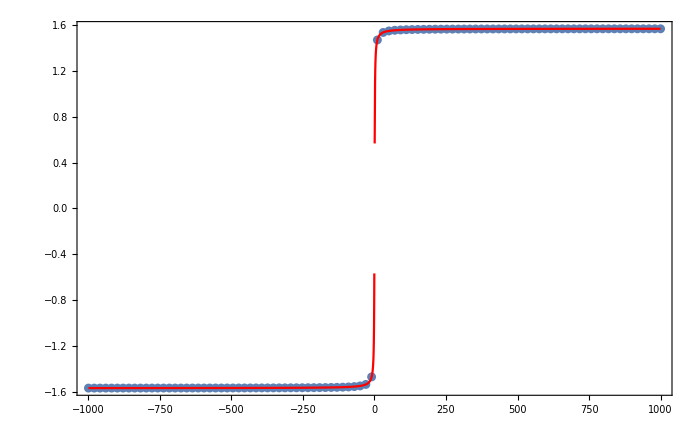

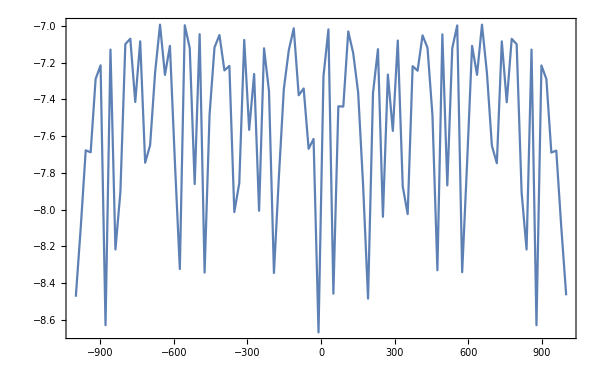

```mathematica
ssefarctan=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_arctan.dat"];
error=Table[{ssefarctan[[i,1]],Log[10,Abs[ArcTan[ ssefarctan[[i,1]]]- ssefarctan[[i,2]]]]}, {i,1,ssefarctan//Length}];
Show[
ListPlot[ssefarctan, PlotRange->All, Frame->True, ImageSize->700],
Plot[ArcTan[x],{x,-1000,1000}, PlotStyle->Red]
]
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```

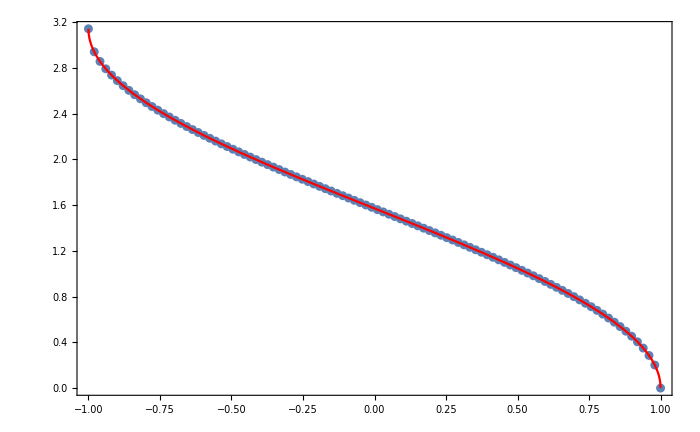

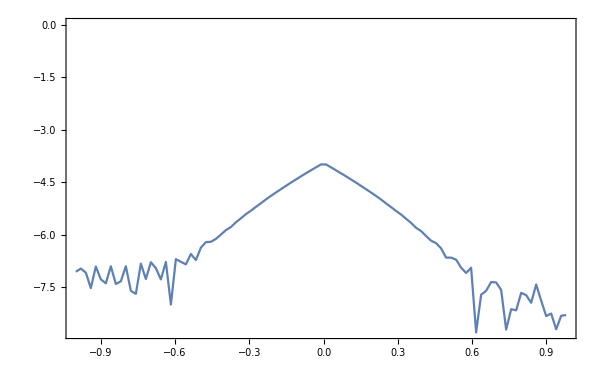

```mathematica
ssefarccos=Import["/home/jure/Documents/opengl_ucenje/testing/data/ssef_arccos.dat"];
error=Table[{ssefarccos[[i,1]],Log[10,Abs[ArcCos[ ssefarccos[[i,1]]]- ssefarccos[[i,2]]]]}, {i,1,ssefarccos//Length}];
Show[
ListPlot[ssefarccos, PlotRange->All, Frame->True, ImageSize->700],
Plot[ArcCos[x],{x,-1,1}, PlotStyle->Red]
]
ListLinePlot[error, ImageSize->600, Frame->True, PlotRange->All]
```